```mathematica
cdata=Import["/Users/benxgh1996/Desktop/Cavendish/cavendish_data.xlsx",{"Data",1}];
```

```mathematica
L=3.53;
```

```mathematica
originalData=cdata;
```

```mathematica
cdata
```

{{0.5,59.},{1.,64.},{1.5,66.8},{2.,69.9},{2.5,73.1},{3.,76.},{3.5,78.4},{4.,80.1},{4.5,80.9},{5.,80.6},{5.5,79.5},{6.,77.6},{6.5,75.4},{7.,72.7},{7.5,70.1},{8.,67.7},{8.5,65.9},{9.,64.5},{9.5,64.},{10.,64.1},{10.5,64.9},{11.,66.3},{11.5,68.2},{12.,70.3},{12.5,72.2},{13.,74.2},{13.5,75.7},{14.,76.7},{14.5,77.2},{15.,77.1},{15.5,76.3},{16.,75.1},{16.5,73.6},{17.5,70.3},{18.,68.8},{18.5,67.6},{19.,66.8},{19.5,66.4},{20.,66.5},{20.5,67.},{21.,68.},{21.5,69.2},{22.,70.5},{22.5,71.8},{23.,73.},{23.5,74.},{24.,74.6},{24.5,74.8},{25.,74.7},{25.5,74.3},{26.,73.5},{26.5,72.6},{27.,71.5},{27.5,70.5},{28.,69.6},{28.5,68.8},{29.,68.3},{29.5,68.1},{30.,68.2},{30.5,68.6},{31.,69.2},{31.5,70.},{32.,70.8},{32.5,71.6},{33.,72.4},{33.5,73.},{34.,73.4},{34.5,73.5},{35.,73.4},{35.5,73.1},{36.,72.6},{36.5,72.},{37.,71.4},{37.5,70.6},{38.,70.},{38.5,69.6},{39.,69.2},{39.5,69.2},{40.,69.2},{40.5,69.5},{41.,69.8},{41.5,70.3},{42.,70.8},{42.5,71.4},{43.,71.8},{43.5,72.2},{44.,72.5},{44.5,72.6},{45.,72.5},{45.5,72.3},{46.,72.},{46.5,71.6},{47.,71.2},{47.5,70.8},{48.,70.4},{48.5,70.1},{49.,69.8},{50.,69.8},{50.5,69.9},{51.,70.2},{51.5,70.5},{52.,70.8},{52.5,71.1},{53.,71.4},{53.5,71.7},{54.,71.9},{54.5,72.},{55.,71.9},{55.5,71.8},{56.,71.6},{56.5,71.4},{57.,71.1},{57.5,70.8},{58.,70.5},{58.5,70.3},{59.,70.2},{59.5,70.2},{60.,70.1},{60.5,70.2},{61.,70.3},{61.5,70.5},{62.,70.8},{62.5,71.},{63.,71.2},{63.5,71.4},{64.,71.5},{64.5,71.5},{65.,71.6},{65.5,71.5},{66.,71.4},{66.5,71.2},{67.,71.1},{67.5,70.9},{68.,70.7},{68.5,70.6},{69.,70.5},{69.5,70.4},{70.,70.4},{70.5,70.3},{71.,70.5},{71.5,70.7},{72.,70.8},{72.5,70.9},{73.,71.1},{73.5,71.2},{74.,71.3},{74.5,71.3},{75.,71.3},{75.5,71.3},{76.,71.2},{76.5,71.1},{77.,71.},{77.5,70.9},{78.,70.8},{78.5,70.7},{79.,70.7},{79.5,70.7},{80.,70.7},{80.5,70.6},{81.,70.7},{81.5,70.8},{82.,70.8},{82.5,70.9},{83.,71.},{83.5,71.1},{84.,71.1},{84.5,71.1},{85.,71.2},{85.5,71.1},{86.,71.1},{86.5,71.},{87.,70.9},{87.5,70.9},{88.,70.8},{88.5,70.8},{89.,70.7},{89.5,70.7},{90.,70.6},{90.5,70.7},{91.,70.7},{91.5,70.7},{92.,70.8},{92.5,70.8},{93.,70.9},{93.5,71.},{94.,71.},{94.5,71.1},{95.,71.1},{95.5,71.1},{96.,71.1},{96.5,71.},{97.,71.},{97.5,70.9},{98.,70.9},{98.5,70.8},{99.,70.8},{99.5,70.7},{100.,70.7},{100.5,70.7},{101.,70.7},{101.5,70.8},{102.,70.8},{102.5,70.8},{103.,70.9},{103.5,70.9},{104.,71.},{104.5,71.},{105.,71.},{105.5,71.},{106.,71.},{106.5,71.},{107.,71.},{107.5,70.9},{108.,70.9},{108.5,70.9},{109.,70.8},{109.5,70.8},{110.,70.8},{110.5,70.8},{111.,70.8},{111.5,70.8},{112.,70.8},{112.5,70.8},{113.,70.9},{113.5,70.9},{114.,70.9},{114.5,70.9},{115.,70.9},{115.5,70.9},{116.,70.9},{116.5,70.9},{117.,70.9},{117.5,70.9},{118.,70.9},{118.5,70.9},{119.,70.9},{119.5,70.8},{120.,70.8},{120.5,70.8},{121.,70.8},{121.5,70.8},{122.,70.8},{122.5,70.8},{123.,70.8},{123.5,70.9},{124.,70.9},{124.5,70.9},{125.,70.9},{125.5,70.9},{126.,70.9},{126.5,70.9},{127.,70.8},{127.5,70.8},{128.,70.8},{128.5,70.8},{129.,70.8},{129.5,70.8},{130.,70.8}}

```mathematica
peaks={{4.5,80.9},{14.5,77.2},{24.5,74.8},{34.5,73.5},{44.5,72.6},{54.5,72},{65,71.6},{75,71.3},{85,71.2},{95.5,71.1},{105.5,71},{116,70.9},{125,70.9}}
```

{{4.5,80.9},{14.5,77.2},{24.5,74.8},{34.5,73.5},{44.5,72.6},{54.5,72},{65,71.6},{75,71.3},{85,71.2},{95.5,71.1},{105.5,71},{116,70.9},{125,70.9}}

```mathematica
peakCopy=peaks
```

{{4.5,80.9},{14.5,77.2},{24.5,74.8},{34.5,73.5},{44.5,72.6},{54.5,72},{65,71.6},{75,71.3},{85,71.2},{95.5,71.1},{105.5,71},{116,70.9},{125,70.9}}

```mathematica
For [i=1,i≤Length[peaks],i++,
peaks[[i]][[1]]*=60;
peaks[[i]][[2]]-=60;
peaks[[i]][[2]]/=(4*353)]
```

```mathematica
peaks
```

{{270.,0.0148017},{870.,0.0121813},{1470.,0.0104816},{2070.,0.00956091},{2670.,0.00892351},{3270.,3/353},{3900,0.0082153},{4500,0.00800283},{5100,0.00793201},{5730.,0.00786119},{6330.,11/1412},{6960,0.00771955},{7500,0.00771955}}

```mathematica
TableForm[%10]
```

270. | 0.0148017
870. | 0.0121813
1470. | 0.0104816
2070. | 0.00956091
2670. | 0.00892351
3270. | 3/353
3900 | 0.0082153
4500 | 0.00800283
5100 | 0.00793201
5730. | 0.00786119
6330. | 11/1412
6960 | 0.00771955
7500 | 0.00771955

```mathematica
N[3/353]
```

0.00849858

```mathematica
N[11/1412]
```

0.00779037

```mathematica
periods = {}
```

{}

```mathematica
For[i=1,i≤Length[peaks]-1,i++,
AppendTo[periods,peaks[[i+1]][[1]]-peaks[[i]][[1]]]]
```

```mathematica
periods
```

{600.,600.,600.,600.,600.,630.,600,600,630.,600.,630.,540}

```mathematica
Mean[periods]
```

602.5

```mathematica
%/60
```

10.0417

```mathematica
peaks
```

{{270.,0.0148017},{870.,0.0121813},{1470.,0.0104816},{2070.,0.00956091},{2670.,0.00892351},{3270.,3/353},{3900,0.0082153},{4500,0.00800283},{5100,0.00793201},{5730.,0.00786119},{6330.,11/1412},{6960,0.00771955},{7500,0.00771955}}

```mathematica
For[i=1,i≤Length[peaks],i++,
peaks[[i]][[1]]/=3600;
peaks[[i]][[2]]*=10^6;]
```

```mathematica
peaks
```

{{0.075,14801.7},{0.241667,12181.3},{0.408333,10481.6},{0.575,9560.91},{0.741667,8923.51},{0.908333,3000000/353},{13/12,8215.3},{5/4,8002.83},{17/12,7932.01},{1.59167,7861.19},{1.75833,2750000/353},{29/15,7719.55},{25/12,7719.55}}

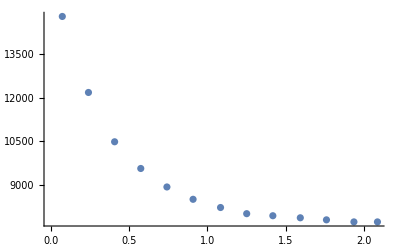

```mathematica
ListPlot[peaks]
```

```mathematica
FindFit[peaks, a ⅇ^(-γ t)+7719.55,{a,γ},t]
```

{a→8641.25,γ→2.71241}

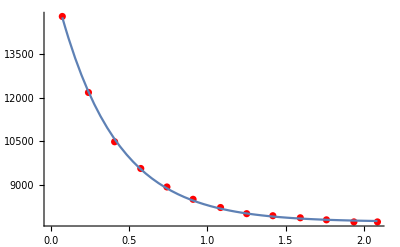

```mathematica
Show[ListPlot[peaks,PlotStyle->Red],Plot[a ⅇ^(-γ t)+7719.55/.{a->8641.250938155199,γ->2.712412588644062},{t,0.075,25/12}]]
```

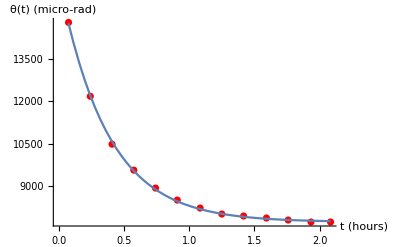

```mathematica
Show[ListPlot[peaks,PlotStyle->Red],Plot[a ⅇ^(-γ t)+7719.55/.{a->8641.250938155199,γ->2.712412588644062},{t,0.075,25/12}],AxesLabel-> {"t (hours)","θ(t) (micro-rad)"}]
```

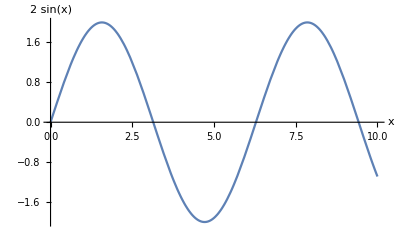

```mathematica
Plot[2 Sin[x],{x,0,10},AxesLabel->{x,2 Sin[x]},LabelStyle->Directive[Blue,Bold]]
```

```mathematica
FindFit[peakCopy, a ⅇ^(-γ t)+b,{a,γ,b},t]
```

{a→12.2023,γ→0.0453835,b→70.9117}

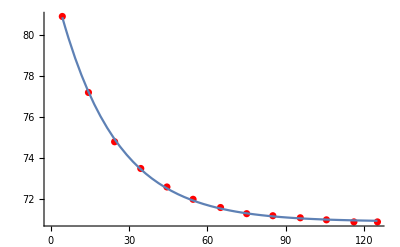

```mathematica
Show[ListPlot[peakCopy,PlotStyle->Red],Plot[a ⅇ^(-γ t)+b/.{a->12.202306942184205,γ->0.04538347314425742,b->70.91173684340716},{t,4.5,125}]]
```

```mathematica
peakCopy
```

{{4.5,80.9},{14.5,77.2},{24.5,74.8},{34.5,73.5},{44.5,72.6},{54.5,72},{65,71.6},{75,71.3},{85,71.2},{95.5,71.1},{105.5,71},{116,70.9},{125,70.9}}

```mathematica
peaksNew=peakCopy
```

{{4.5,80.9},{14.5,77.2},{24.5,74.8},{34.5,73.5},{44.5,72.6},{54.5,72},{65,71.6},{75,71.3},{85,71.2},{95.5,71.1},{105.5,71},{116,70.9},{125,70.9}}

```mathematica
s
```

10.85

```mathematica
L
```

353

```mathematica
For[i=1,i≤Length[peaksNew],i++,
peaksNew[[i]][[1]]/=60;
peaksNew[[i]][[2]]=(-peaksNew[[i]][[2]])/(2L)+s/(4L)]
```

```mathematica
peaksNew
```

{{0.075,-0.106905},{0.241667,-0.101664},{0.408333,-0.0982649},{0.575,-0.0964235},{0.741667,-0.0951487},{0.908333,-0.0942989},{13/12,-0.0937323},{5/4,-0.0933074},{17/12,-0.0931657},{1.59167,-0.0930241},{1.75833,-0.0928824},{29/15,-0.0927408},{25/12,-0.0927408}}

```mathematica
TableForm[%77]
```

0.075 | -0.106905
0.241667 | -0.101664
0.408333 | -0.0982649
0.575 | -0.0964235
0.741667 | -0.0951487
0.908333 | -0.0942989
13/12 | -0.0937323
5/4 | -0.0933074
17/12 | -0.0931657
1.59167 | -0.0930241
1.75833 | -0.0928824
29/15 | -0.0927408
25/12 | -0.0927408

```mathematica
peaksNew={{0.075,-0.10690509915014165},{0.24166666666666667,-0.10166430594900851},{0.4083333333333333,-0.09826487252124647},{0.575,-0.09642351274787536},{0.7416666666666667,-0.09514872521246459},{0.9083333333333333,-0.09429886685552408},{13/12,-0.09373229461756374},{5/4,-0.09330736543909349},{17/12,-0.09316572237960341},{1.5916666666666666,-0.0930240793201133},{1.7583333333333333,-0.09288243626062323},{29/15,-0.09274079320113315},{25/12,-0.09274079320113315}}
```

{{0.075,-0.106905},{0.241667,-0.101664},{0.408333,-0.0982649},{0.575,-0.0964235},{0.741667,-0.0951487},{0.908333,-0.0942989},{13/12,-0.0937323},{5/4,-0.0933074},{17/12,-0.0931657},{1.59167,-0.0930241},{1.75833,-0.0928824},{29/15,-0.0927408},{25/12,-0.0927408}}

```mathematica
γ=.
```

```mathematica
FindFit[peaksNew,A ⅇ^(-γ t)-0.09274079320113315,{A,γ},t]
```

{A→-0.0172825,γ→2.71241}

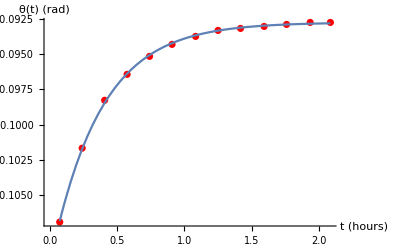

```mathematica
Show[ListPlot[peaksNew,PlotStyle->Red],Plot[A ⅇ^(-γ t)-0.09274079320113315/.{A->-0.017282501379125192,γ->2.712408435890985},{t,0.075,25/12}],AxesLabel-> {"t (hours)","θ(t) (rad)"}]
```

```mathematica
2.71241/3600
```

0.000753447

```mathematica
ScientificForm[0.0007534472222222223]
```

7.53447×10^-4

```mathematica
T=602.5
```

602.5

```mathematica
γ=7.53447*10^-4
```

0.000753447

```mathematica
s=10.85
```

10.85

```mathematica
L=353
```

353

```mathematica
d=0.05
```

0.05

```mathematica
b=0.047
```

0.047

```mathematica
r=0.0075
```

0.0075

```mathematica
m1=1.5
```

1.5

```mathematica
β=b^3/((b^2+4 d^2)^(3/2))
```

0.0769615

```mathematica
(((2π)/T)^2+γ^2)*s/L*1/4*(d^2+2/5 r^2)*b^2/(m1 d)*1/(1-β)
```

6.76157×10^-11

```mathematica
{T,γ,s,L,d,r,b,m1}
```

{602.5,0.000753447,10.85,353,0.05,0.0075,0.047,1.5}

```mathematica
(2π)/T
```

0.0104285

```mathematica
(((2π)/T)^2+γ^2)*2*0.02*(d^2+2/5 r^2)
```

1.10306×10^-8

```mathematica
1/(1-β)
```

1.08338

```mathematica
9.8/(4/3 π (5.448*1000)*(12740640/2))
```

6.74123×10^-11

```mathematica
998.23*5.48
```

5470.3